# Quantum Brownian Motion

## References

Path integral approach to quantum Brownian motion, by Caldeira and Leggett

["Reduction of a wave packet in quantum Brownian motion by Unruh and Zurek"](https://journals-aps-org.ezp.sub.su.se/prd/abstract/10.1103/PhysRevD.40.1071)

## Gaussian integral identity

-Graphics-
-Graphics-

## Keldysh path integral for coherent bosons in a single quantum level

See Kamenev’s book, chapter 2 and 3

### Partition function definition

Define:

ρ̂ is an initial density matrix. We will choose it to be in thermal eq:
-Graphics- (notice that it is not normalized to unity)
and the unitary evolution operator:
-Graphics-

The trace is cyclic, and adding an identity operator expanded in a complete basis, i.e. OverHat[1]=∑_(i,j=1)^N |ϕ_i⟩  ⟨ϕ_i|,
and using the trace of a scalar is a scalar, then we have:
	 Tr A B=∑_(i,j=1)^N ⟨ϕ_j|A|ϕ_i⟩⟨ϕ_i|B|ϕ_j⟩

### Hamiltonian for bosonic particles in a single quantum state with energy ω_0

Consider:
-Graphics-=ω_0 N̂
then
-Graphics-,-Graphics-

### Path Integral steps

In order to derive the path integral formulation, let's divide the contour in the following way:
	-Graphics-

First, let's insert the over-complete coherent state basis:
	-Graphics-
at the initial and final states, then commute the integrals with the trace and then use the cyclic property of the trace:
	Tr U_C ρ  = ∫d[(ϕ̄)_1,ϕ_1]∫d[(ϕ̄)_(2N),ϕ_(2N)]ⅇ^(-|ϕ_1|^2-|ϕ_(2N)|^2) ⟨ϕ_1|U_c|ϕ_(2N)⟩    ⟨ϕ_(2N)|ρ|ϕ_1⟩ 

We can insert the over-complete basis at discrete infinitesimal time intervals, in order to derive the path integral:
For example, for N=3:
	-Graphics-
or more generally:
	⟨ϕ_1|(ρ̂)_0|ϕ_(2N)⟩ 
{ ∏_(j=1)^(N-1) ⟨ϕ_(j+1)|(Û)_δ_t|ϕ_j⟩}
⟨ϕ_N|1|ϕ_(N+1)⟩  
{∏_(j=N)^(2N-1) ⟨ϕ_(j+1)|(Û)_-δ_t|ϕ_j⟩}
Up to linear order in δ_t:
	-Graphics-
This actually applies to any normally-ordered H. -> Other examples? 

Use the identity:
	⟨ϕ_1|(ρ̂)_0|ϕ_(2N)⟩=exp{(ϕ̄)_1 ϕ_(2N)ρ(ω_0)}
and that
	-Graphics-
we derive the partition function below.

### Partition function discrete

-Graphics-
Note that G is non-diagonal, and it depends on the Hamiltonian. 
For N=3:
 -Graphics-, -Graphics-
Its inverse gives the 2-pt correlation functions.

### 2-pt correlation functions, discrete

-Graphics-
 For N=3, we get
 -Graphics-, ρ=ρ(ω_0)

### 2-pt correlation functions in the continuum limit: N→ ∞, ϕ_i→ ϕ(t)

Determinant in the continuum limit:
	-Graphics-
2-pt functions (+ and - indicate the positive and the negative branches of the Keldysh contour.):
	-Graphics-
where the bosonic occupation number is:
	-Graphics-

### Green functions in the continuum limit and Keldysh space

Keldysh rotation:
	-Graphics-
2-pt correlation functions:
	-Graphics-
	-Graphics-
	-Graphics-
Properties 
	-Graphics-

### Fluctuation-Dissipation Theorem: G^K(ϵ)=Coth[(ϵ-μ)/(2 T)](G^R(ϵ)-G^A(ϵ))

For a thermal initial state, 
	n_B=1/(e^((ϵ-μ)/T)-1)
and using the delta identity:
	∫_(-∞)^∞ e^(ⅈ ω t)ⅆt = 2 π δ(ω) =ⅈ(1/(ω +ⅈ 0)-1/(ω -ⅈ 0))
	∫_0^∞ e^((ⅈ ω-0) t)ⅆt =ⅈ/(ω +ⅈ 0)
	∫_(-∞)^0 e^((ⅈ ω+0) t)ⅆt =-ⅈ/(ω -ⅈ 0)
we can rewrite:
	G^K(ϵ)=-2π ⅈ (2/(e^((ϵ-μ)/T)-1)+1)δ(ϵ-ω_0)
	=- ⅈ ((e^((ϵ-μ) /T)+1)/(e^((ϵ-μ)/T)-1))ⅈ(1/(ϵ-ω_0 +ⅈ 0)-1/(ϵ-ω_0 -ⅈ 0))
	=Coth[(ϵ-μ)/(2 T)](G^R(ϵ)-G^A(ϵ))

### Nonlinear Fluctuation-Dissipation Theorem

Higher order correlation functions in Keldysh space are not all independent of each other, just like in the 2-pt case. See:

[A Generalized Fluctuation-Dissipation Theorem for NonlinearResponse Functions](https://arxiv.org/pdf/hep-th/9809016.pdf)

### Partition function in the continuum limit

Partition function is formally:
	-Graphics-	

The naive way gives a non-interacting action. Taking into account the 2-pt correlation functions: 
	-Graphics-

## Keldysh action for the harmonic oscillator

### Classical action along the Keldysh contour S[X^cl, x^q]=2∫_C dt ((Ẋ)^cl(Ẋ)^q-ω_0^2 X^cl X^q)

Single particle in an arbitrary potential, where C is the Keldysh closed time contour:
-Graphics-
Splitting the contour in the + and - branches:
	S[X_+, x_-]=∫_(-∞)^∞ ⅆt [2(Ẋ)^cl(Ẋ)^q-V(X_+)+V(X_-)]
then do the Keldysh rotation:
-Graphics-
The action becomes ()after a partial integration for the 1st term):
-Graphics-

#### Harmonic oscillator

V(X)=ω_0/2 X^2
S[X^cl, x^q]=2∫_C dt ((Ẋ)^cl(Ẋ)^q-ω_0^2 X^cl X^q)

#### Small X^q expansion

-Graphics-
V’(X) is derivative respective X

### Keldysh action S[X^cl,X^q]=2∫_(-∞)^∞ ⅆt ((Ẋ)^cl(Ẋ)^q-ω_0^2 X^cl X^q+1/4 X^q D^(-1K) X^q)

The Keldysh action takes into account the 2-pt correlation between the fields of the different branches (see the previous section, where the structure of the action applies here too):
	-Graphics-
	-Graphics-

#### Green functions for the harmonic oscillator

-Graphics-

In Fourier space:
-Graphics-
-Graphics-

D^K(ϵ)=1/2 Coth(ϵ/(2 T))[1/((ϵ+ⅈ 0)^2-ω_0^2)-1/((ϵ-ⅈ 0)^2-ω_0^2)]-> In time space? The textbook says it's only a regularization...

#### Action for the harmonic oscillator

D^-1 X=(D^(-1A) X^q, D^(-1R) X^cl+D^(-1K) X^q)
	=2(-(X^(..))^q-ω_0^2 X^q, -(X^(..))^cl-ω_0^2 X^cl+1/2 D^(-1K) X^q)

1/2 X^T D^-1 X =(-X^cl(X^(..))^q-ω_0^2 X^cl X^q-X^q (X^(..))^cl-ω_0^2 X^q X^cl+1/2 X^q D^(-1K) X^q)
		{d/dt(X^cl(Ẋ)^q)=(Ẋ)^cl(Ẋ)^q+X^cl(X^(..))^q, d/dt((Ẋ)^cl X^q)=(Ẋ)^cl(Ẋ)^q+(X^(..))^cl X^q}
                   → 2((Ẋ)^cl(Ẋ)^q-ω_0^2 X^cl X^q+1/4 X^q D^(-1K) X^q)

The last term in red is an additional term that corrects the action if the continuum limit is done naively. It's of higher order in X^q, so it can be ignored in the semiclassical limit.

#### Quartic potential?

V(X) =λ X^4
V(X_+=X^cl+X^q)-V(X_-=X^cl-X^q)=8λ (X^(cl 3)X^q+X^cl X^(q 3))

```mathematica
(xc+xq)^4-(xc-xq)^4//Expand
```

8 xc^3 xq+8 xc xq^3

## Single particle linearly coupled with a bath

### Action

Note that S_p in the book is the classical action of the single particle! I think the Keldysh action should be used, and for the harmonic oscillator (see previous section):
	S_p[X^cl,X^q]=2∫_(-∞)^∞ ⅆt  ((Ẋ)^cl(Ẋ)^q-ω_0^2 X^cl X^q+1/4 X^q D^(-1K) X^q)

-Graphics-
σ_1is the Pauli matrix in Keldysh space

### Effective action for the single particle

S[X^cl,X^q]=1/2∫_(-∞)^∞ ⅆt  (X(t))^T D^-1(t)X(t)+1/2∫∫_(-∞)^∞ ⅆtⅆt'  X^T(t)𝔇^-1(t-t') X(t')
		=1/2∫∫_(-∞)^∞ ⅆtⅆt'  X^T(t){D^-1(t)δ(t-t')+𝔇^-1(t-t') }X(t')
where
	-Graphics-
	
We have integrated out S_bath+S_int using a Gaussian integral identity.

Using the results from the single harmonic oscillator in a previous section, we get for the bath:
	𝔇^-1=(0 | [𝔇^-1]^A
[𝔇^-1]^R | [𝔇^-1]^K)=∑_s g_s^2(0 | -1/([D_s^-1]^A)
-1/([D_s^-1]^R) | ([D_s^-1]^K)/(([D_s^-1]^R [D_s^-1])^A)) (in time space)

#### Computation details

```mathematica
{Xc,Xq}.({{0, DinvA}, {DinR, DinvK}}).{Xc,Xq}//Simplify
```

Xq (DinR Xc+DinvA Xc+DinvK Xq)

```mathematica
Dinv=({{0, DinvA}, {DinR, DinvK}});
Dmatrix=Inverse@Dinv;
%//MatrixForm
-PauliMatrix[1].Dmatrix.PauliMatrix[1]//MatrixForm
```

(-DinvK/(DinR DinvA) | 1/DinR
1/DinvA | 0)

(0 | -1/DinvA
-1/DinR | DinvK/(DinR DinvA))

### In Fourier space?

-Graphics-
-Graphics-

[D_s^-1(t)]^(R,A)=2((ⅈ ∂_t ± ⅈ 0)^2-ω_s^2)  
[𝔇^-1(t)]^(R,A)=-∑_s g_s^2 1/([D_s^-1]^(R,A))

[D_s^-1(ϵ)]^(R,A)=2((ϵ ± ⅈ 0)^2-ω_s^2)-> [D_s(ϵ)]^(R,A)=2((ϵ ± ⅈ 0)^2-ω_s^2)^-1
[𝔇^-1(ϵ)]^(R,A)=-∑_s g_s^2 2((ϵ ± ⅈ 0)^2-ω_s^2)^-1=∫_0^∞ ⅆω/(2 π)ω J(ω)  1/(ω^2-(ϵ ± ⅈ 0)^2)

[𝔇^-1(t)]^(R,A)=∓∫_0^∞ ⅆω J(ω) Sin[t ω]
	∫_(-∞)^∞ ⅆϵ 1/(ω^2-(ϵ ± ⅈ 0)^2)Exp[ⅈ ϵ t] = ∫_(-∞)^∞ ⅆϵ 1/((ϵ ± ⅈ 0)+ω)-1/((ϵ ± ⅈ 0)-ω)Exp[ⅈ ϵ t]=∓(2 π Sin[t ω])/ω
	(∫_(-∞)^∞ ⅆϵ 1/(ω^2-(ϵ ± ⅈ 0)^2)Exp[-ⅈ ϵ t]=±(2 π Sin[t ω])/ω)
		poles
			ϵ_+=ω ∓ ⅈ 0
			ϵ_-=-ω ∓ ⅈ 0
		when the poles are in the lower half plane, then there's a global negative sign  because of the orientation

[𝔇^-1(t)]^R+[𝔇^-1(t)]^A=0
[𝔇^-1(t)]^R-[𝔇^-1(t)]^A=-2∫_0^∞ ⅆω J(ω) Sin[t ω]

How to compute the K-component?
[D_s(ϵ)]^K=Coth(ϵ/T)([D_s(ϵ)]^R-[D_s(ϵ)]^A)
[𝔇^-1(ϵ)]^K=∑_s g_s^2([D_s^-1]^K)/(([D_s^-1]^R [D_s^-1])^A)=∑_s g_s^2 1/((([D_s^-1]^R [D_s^-1])^A[D_s])^K)
		=∑_s g_s^2 1/(([D_s^-1]^R [D_s^-1])^A)1/(Coth(ϵ/T)([D_s]^R-[D_s]^A))
		=∑_s g_s^2 1/(Coth(ϵ/T)([D_s^-1]^A-[D_s^-1]^R))
		=∑_s g_s^2 1/(Coth(ϵ/T)(2((ϵ - ⅈ 0)-ω)-2((ϵ + ⅈ 0)-ω)))=∑_s g_s^2-1/(Coth(ϵ/T)4  ⅈ 0) ?

𝔇^K(ϵ)=Coth[ϵ/(2 T)](𝔇^R(ϵ)-𝔇^A(ϵ))

#### Computation

```mathematica
2π ⅈ Plus@@{Residue[Exp[ⅈ ϵ t]/(ω^2-(ϵ+ⅈ x)^2),{ϵ,-ω-ⅈ x}],Residue[Exp[ⅈ ϵ t]/(ω^2-(ϵ+ⅈ x)^2),{ϵ,ω-ⅈ x}]}/.x->0
%//FullSimplify
2π ⅈ Plus@@{Residue[Exp[ⅈ ϵ t]/(ω^2-(ϵ-ⅈ x)^2),{ϵ,-ω+ⅈ x}],Residue[Exp[ⅈ ϵ t]/(ω^2-(ϵ-ⅈ x)^2),{ϵ,ω+ⅈ x}]}/.x->0
%//FullSimplify
```

2 ⅈ π (ⅇ^(-ⅈ t ω)/(2 ω)-ⅇ^(ⅈ t ω)/(2 ω))

(2 π Sin[t ω])/ω

2 ⅈ π (ⅇ^(-ⅈ t ω)/(2 ω)-ⅇ^(ⅈ t ω)/(2 ω))

(2 π Sin[t ω])/ω

### Solution for the Ohmic bath

Assuming continuous spectrum for the bath and that it’s ohmic, i.e.
	-Graphics-

Then we get:

	-Graphics-
At high T limit, the local term is the leading one.

#### Ohmic bath computation details

-Graphics-
-Graphics- const may be obmitted
-Graphics-
Inverse FT the expressions above
	-Graphics- -> gives dissipation
	-Graphics--> gives noise fluctuation
	-Graphics- satisfies the condition
	-Graphics-

[D_eff^-1]^(R,A)(t-t')=[D^-1]^(R,A)(t)δ(t-t')+[𝔇^-1]^(R,A)(t-t')
			=2[(ⅈ∂_t ± ⅈ 0)^2-ω_0^2∓ γ ∂_t']δ(t-t') 


[D_eff^-1]^K(t-t')=[D^-1]^K(t)δ(t-t')+[𝔇^-1]^K(t-t')
			=4 ⅈ γ [(2 T+C) δ(t-t')-(π T^2)/(Sinh(π T (t-t')))]

	D^K(ϵ)=1/2 Coth(ϵ/(2 T))[1/((ϵ+ⅈ 0)^2-ω_0^2)-1/((ϵ-ⅈ 0)^2-ω_0^2)]?

```mathematica
Series[Coth[x],{x,0,1}]
```

1/x+x/3+O[x]^2

##### High T limit

[𝔇^-1(t-t')]^K≈8 ⅈ γ T δ(t-t')
	T^2/Sinh[π T t]^2=(2 T^2)/(-1+1/2 ⅇ^(-2 π t T)+1/2 ⅇ^(2 π t T))≈4 T^2 ⅇ^(-2 π t T)

## Effective field approach: a free particle interacting with a bath

```mathematica
["Hong-Liu's lecture notes"](https://arxiv.org/pdf/1805.09331.pdf), page 12
```

Note that the particle here is free, namely V(X)=0. However, when the guess the L_EFT, the use general arguments, and do get a term that actually would correspond to the harmonic potential. See more comments below.

```mathematica
-Graphics-
-Graphics-
```

Comparing the above result with the exact result in the previous section, we see that:
	The c x_a x_r term comes from a quadratic potential, but Hong Liu says it’s an effective potential induced by the bath?
	The ν x_a (ẋ)_r and the i/2 σ x_a^2 terms come from integrating out the bath.
	The M̃(ẋ)_a (ẋ)_r term comes from the kinetic term.

Most general terms :
x_a^2 → gives rise the Gaussian noise
x_r^2 → Not there, because of the Lagrangian? ...
x_a x_r
(ẋ)_a x_r → Not there
x_a(ẋ)_r
(ẋ)_a(ẋ)_r

```mathematica
Series[1/(1-x),{x,0,1}]
```

1+x+O[x]^2

### Remark for higher order terms

### Cubic terms

Most general terms :
x_a^3
x_r^3 → should not be there
x_a^2 x_r
x_a x_r^2
((ẋ)_a)^2 x_r
x_a((ẋ)_r)^2
(ẋ)_a x_r^2
x_a^2(ẋ)_r
((ẋ)_a)^2(ẋ)_r
(ẋ)_a((ẋ)_r)^2

### Stochastic equation for some cubic terms such that the noise is Gaussian

Legendre transformation to get the Gaussian noise ξ :

Then, the argument of the exponential is:
	-c x_a x_r -ν x_a (ẋ)_r+M̃(ẋ)_a (ẋ)_r+i/(2σ) ξ^2+ξ x_a
- α x_a x_r^2 - β x_a((ẋ)_r)^2- γ (ẋ)_a x_r^2 
	
For simplicity, we consider non-linear interactions that are linear in x_a, as shown in the line above.
Now, we can derive the SDE:
	c  x_r +ν (ẋ)_r+M̃(x^(..))_r+α x_r^2+β ((ẋ)_r)^2-2γ x_r(ẋ)_r=ξ
What are the meanings of the new terms? Are they physical?

### Non Gaussian noise?

## Linear QBM exact quantum master eq

### Setting

Master equation is the time evolution of the (reduced) density matrix:
-Graphics-
The goal is to find H_ρ operator.

#### Feynman-Vernon

Assuming the initial density matrix can be factorized to the one of the Brownian motion particle, i.e. ρ_r, and that of the bath, 
-Graphics-
then:
-Graphics-
where J_r is an evolution operator, with the path-integral representation:
-Graphics-
F[x,x'] is called the influence functional, which contains the bath dof and the interaction with the bath (it contains the initial bath density matrix too).
The bath's initial density matrix will be assumed to be in thermal eq.

#### Action

-Graphics-

#### Spectral density: I(ω)=2/π Μ γ_0 ω (ω/(ω̃))^(n-1)Exp[-ω^2/Λ^2]

The spectral density is defined as:
-Graphics-
We study the ones that have the shape:
-Graphics-

{{√10 ⅇ^(-ω^2/100) √ω,ⅇ^(-ω^2/100) ω,1/100 ⅇ^(-ω^2/100) ω^3}}

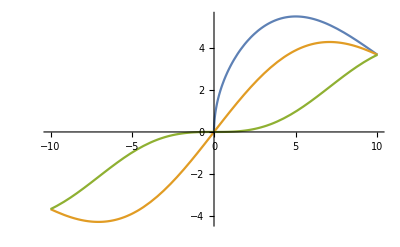

```mathematica
ω (ω/Λ)^{n-1} Exp[-ω^2/Λ^2]/.n->{1/2,1,3}/.Λ->10
Plot[Evaluate@%,{ω,-10,10}]
```

### Influence functional, fluctuation-dissipation η(s)=-∫_0^∞ ⅆω I(ω) sin(ω s) ν(s)=∫_0^∞ ⅆω I(ω) coth(1/2 β ℏ ω) cos(ω s)

ln F[x,x']=-ⅈ/ħ ∫_0^t ds_1∫_0^s_1 ds_2{x_q(s_1)η(s_1-s_2) x_cl(s_2) -ⅈ x_q(s_1)ν(s_1-s_2) x_q(s_2)}

Noise or fluctuation kernel is non-local in general:
-Graphics-

Dissipation kernel: η(s)=-∫_0^∞ ⅆω I(ω)  sin(ω s)
-Graphics-, -Graphics-

Fluctuation-dissipation relation:
-Graphics-

#### Check the FD relation?

⋁[ω,s]=I[ω]Coth[1/2 β ℏ ω]Cos[ω s]
K[ω,s]=ω/π Coth[1/2 β ℏ ω]Cos[ω s]
γ[ω,s]=1/ω I[ω]Cos[ω s]

⋁[ω,s]=π K[ω,s]γ[ω,s] /Cos[ω s]
=∫_(-∞)^∞ ⅆs' ∫_0^∞ ⅆω' K[ω,s-s']γ[ω',s']

⋁[s]=∫_(-∞)^∞ ⅆs'  K[s-s']γ[s']
	=∫_(-∞)^∞ ⅆs'∫_0^∞ ⅆω ∫_0^∞ ⅆω' K[ω,s-s']γ[ω',s']
	=∫_(-∞)^∞ ⅆs'∫_0^∞ ⅆω ∫_0^∞ ⅆω' ω/π Coth[1/2 β ℏ ω]Cos[ω (s-s')]1/ω' I[ω']Cos[ω' s']
	=∫_0^∞ ⅆω ∫_0^∞ ⅆω' ω/π Coth[1/2 β ℏ ω]1/ω' I[ω']∫_(-∞)^∞ ⅆs'Cos[ω (s-s')]Cos[ω' s']

### High T limit ν(s)=2/(β ℏ) γ(s)=2/(β ℏ)∫_0^∞ ⅆω (I(ω))/ω cos(ω s) η(s)=γ'(s)=-∫_0^∞ ⅆω I(ω) sin(ω s)

Classical or high T limit:
	-Graphics-

Derivation:
	coth(1/2 β ℏ ω) ≈2/(β ℏ ω) +O(β)=(2 T)/(ℏ ω)

K(s)=∫_0^∞ ⅆω/π ω  coth(1/2 β ℏ ω) cos(ω s)
	≈1/π  2/(β ℏ)∫_0^∞ ⅆω cos(ω s)
	=1/π  1/(β ℏ)2π δ(s)=2/(β ℏ) δ(s)
ν(s)=∫_(-∞)^∞ ds' K(s-s') γ(s')
	≈2/(β ℏ)∫_(-∞)^∞ ds' δ(s-s') γ(s')=2/(β ℏ) γ(s)

```mathematica
Series[Coth[x],{x,0,1}]
```

1/x+x/3+O[x]^2

### Exact quantum master equation

-Graphics-

#### Coefficients

-Graphics-
u and v are classical solutions, see the paper
-Graphics-
-Graphics-

#### High T limit of the coefficients: why doesn’t the 2nd diffusion term go to 0 for ohmic case?

```mathematica
-Graphics--Graphics-
```

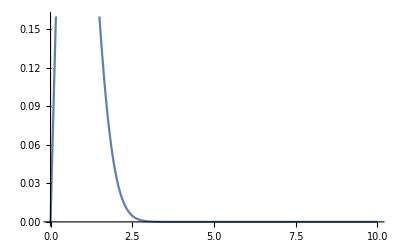

```mathematica
Plot[Λ Exp[-Λ^2],{Λ,0,10}]
```

### Exact Wigner equation

This paper corrects the equation above adding ħ in front of the diffusion coefs.
["https://arxiv.org/pdf/quant-ph/9508004.pdf"](https://arxiv.org/pdf/quant-ph/9508004.pdf)

### Langevin eqs

#### FP coefficients

D_q=p
D_p=-(Ω^2+(δΩ(t))^2) q-Γ(t) p
D_pp=2 ħ Γ(t) h(t)
D_pq=D_qp=-ħ Γ(t) f(t)

#### FP <-> Langevin

Risken book, chapter 3.4.
Langevin to FP transformation below determines uniquely Ds:
	-Graphics-
	-Graphics-
	
FP to Langevin (with white noise) is not unique for N>1. For N=2 case, which is our case, there’s an additional degree of freedom. 
In the eigenbasis of the diffusion matrix:
	-Graphics-
In our case the diffusion matrix doesn’t depend on the (q, p), and we denote the eigenbasis with ', hence
	h'_i=D'_i
g'_(i j)= √(D'_(i j))

#### Eigenbasis

D=(0 | D_qp
D_qp | D_pp)
λ_±=1/2 (D_pp±√(D_pp^2+4 D_qp^2)) 
v_±={-λ_∓/D_qp,1}
Λ=( v_- v_+)=(-λ_+/D_qp | -λ_-/D_qp
1 | 1)
D'=Λ^T D Λ -> D =(Λ^-1)^T D' Λ^-1
g'=√D' -> g = (Λ^-1)^T g' Λ^-1 -> the structure is not the same as D, namely g_11!=0 in general. Can we rotate it away?


D_(1)'=Λ^T D_(1)=h'
h = (Λ^-1)^T h'=D_(1)

##### Computations

```mathematica
Inverse@({{Λ1, Λ2}, {1, 1}})//MatrixForm
```

(1/(Λ1-Λ2) | -Λ2/(Λ1-Λ2)
-1/(Λ1-Λ2) | Λ1/(Λ1-Λ2))

```mathematica
dm=({{0, Dqp}, {Dqp, Dpp}});
ee=Eigenvalues@dm
ev=Eigenvectors@dm
```

{1/2 (Dpp-√(Dpp^2+4 Dqp^2)),1/2 (Dpp+√(Dpp^2+4 Dqp^2))}

{{-(Dpp+√(Dpp^2+4 Dqp^2))/(2 Dqp),1},{-(Dpp-√(Dpp^2+4 Dqp^2))/(2 Dqp),1}}

```mathematica
toλRule={(Plus@@ee//Simplify)-> λ1+λ2,(ee[[2]]-ee[[1]]//Simplify)-> λ2-λ1}
invλRule={λ1-> ee[[1]],λ2->ee[[2]]}
λ1 λ2/.invλRule//FullSimplify
toλRule=Append[toλRule,-%-> -λ1 λ2]
```

{Dpp→λ1+λ2,√(Dpp^2+4 Dqp^2)→-λ1+λ2}

{λ1→1/2 (Dpp-√(Dpp^2+4 Dqp^2)),λ2→1/2 (Dpp+√(Dpp^2+4 Dqp^2))}

-Dqp^2

{Dpp→λ1+λ2,√(Dpp^2+4 Dqp^2)→-λ1+λ2,Dqp^2→-λ1 λ2}

```mathematica
evλ=ev/.toλRule
norms=({evλ[[1]].evλ[[1]],evλ[[2]].evλ[[2]]}//Simplify)
nevλ=Assuming[Dpp>0&&Dqp>0,evλ/√norms/.toλRule//FullSimplify]
```

{{-λ2/Dqp,1},{-λ1/Dqp,1}}

{1+λ2^2/Dqp^2,1+λ1^2/Dqp^2}

{{-λ2/(√(Dqp^2+λ2^2)),Dqp/(√(Dqp^2+λ2^2))},{-λ1/(√(Dqp^2+λ1^2)),Dqp/(√(Dqp^2+λ1^2))}}

```mathematica
nevλ.dm.Transpose[nevλ]/{λ1,λ2}/.toλRule/.invλRule//FullSimplify
```

{{1,0},{0,1}}

```mathematica
inevλ=Assuming[Dpp>0&&Dqp>0,Inverse@nevλ//FullSimplify]/.toλRule//Simplify
```

{{(√(λ2 (-λ1+λ2)))/(λ1-λ2),(√(λ1 (λ1-λ2)))/(-λ1+λ2)},{(λ1 √(λ2 (-λ1+λ2)))/(Dqp (λ1-λ2)),(√(λ1 (λ1-λ2)) λ2)/(Dqp (-λ1+λ2))}}

```mathematica
gd=DiagonalMatrix@{√λ1,√λ2}
Assuming[Dpp>0&&Dqp>0,inevλ.gd.Transpose@inevλ//FullSimplify]
%/.invλRule//Simplify
```

{{√λ1,0},{0,√λ2}}

{{√λ1-λ1/(√λ1+√λ2),-(λ1 λ2)/(Dqp √λ1+Dqp √λ2)},{-(λ1 λ2)/(Dqp √λ1+Dqp √λ2),-(λ1 λ2 (λ1+√λ1 √λ2+λ2))/(Dqp^2 (√λ1+√λ2))}}

{{(√(Dpp-√(Dpp^2+4 Dqp^2)) √(Dpp+√(Dpp^2+4 Dqp^2)))/(√2 (√(Dpp-√(Dpp^2+4 Dqp^2))+√(Dpp+√(Dpp^2+4 Dqp^2)))),(√2 Dqp)/(√(Dpp-√(Dpp^2+4 Dqp^2))+√(Dpp+√(Dpp^2+4 Dqp^2)))},{(√2 Dqp)/(√(Dpp-√(Dpp^2+4 Dqp^2))+√(Dpp+√(Dpp^2+4 Dqp^2))),(2 Dpp+√(Dpp-√(Dpp^2+4 Dqp^2)) √(Dpp+√(Dpp^2+4 Dqp^2)))/(√2 (√(Dpp-√(Dpp^2+4 Dqp^2))+√(Dpp+√(Dpp^2+4 Dqp^2))))}}

```mathematica
RotationMatrix[θ].({{a, c}, {c, d}}).Transpose@RotationMatrix[θ]//FullSimplify
Solve[%[[1,1]]==0,θ]//FullSimplify
```

{{a Cos[θ]^2-2 c Cos[θ] Sin[θ]+d Sin[θ]^2,c Cos[2 θ]+(a-d) Cos[θ] Sin[θ]},{c Cos[2 θ]+(a-d) Cos[θ] Sin[θ],d Cos[θ]^2+a Sin[θ]^2+c Sin[2 θ]}}

{{θ→ConditionalExpression[2 π C[1]-ⅈ Log[-(ⅈ (c^2-ⅈ c d+√(c^4-a c^2 d)) √(d^2/(2 c^2-a d+d^2+2 √(c^4-a c^2 d))))/(c d)], C[1]∈ℤ]},{θ→ConditionalExpression[2 π C[1]-ⅈ Log[((c (ⅈ c+d)+ⅈ √(c^4-a c^2 d)) √(d^2/(2 c^2-a d+d^2+2 √(c^4-a c^2 d))))/(c d)], C[1]∈ℤ]},{θ→ConditionalExpression[2 π C[1]-ⅈ Log[(ⅈ (-c^2+ⅈ c d+√(c^4-a c^2 d)) √((2 c^2-a d+d^2+2 √(c^4-a c^2 d))/(4 c^2+(a-d)^2)))/(c d)], C[1]∈ℤ]},{θ→ConditionalExpression[2 π C[1]-ⅈ Log[((c (ⅈ c+d)-ⅈ √(c^4-a c^2 d)) √((2 c^2-a d+d^2+2 √(c^4-a c^2 d))/(4 c^2+(a-d)^2)))/(c d)], C[1]∈ℤ]}}

#### Wrong

q̇= p+√(- ħ Γ(t) f(t))ξ_p
ṗ=-(Ω^2+(δΩ(t))^2)q-Γ(t) p+√(ħ Γ(t) f(t))ξ_p+√(-ħ Γ(t) f(t)) ξ_q

q^(..)= -(Ω^2+(δΩ(t))^2)q
	-Γ(t) (q̇-√(- ħ Γ(t) f(t))ξ_p)
          +√(2ħ Γ(t) h(t))ξ_p+√(-ħ Γ(t) f(t)) (ξ_q+ξ_p)+∂/(∂t)(√(-ħ Γ(t) f(t))ξ_p)
Assume
	q^(..) ≈0
then
Γ(t) q̇=-(Ω^2+(δΩ(t))^2)q
	      + (Γ(t) √(- ħ Γ(t) f(t))+√(2ħ Γ(t) h(t))+√(-ħ Γ(t) f(t))+∂/(∂t)(√(-ħ Γ(t) f(t))))ξ_p
                   +√(-ħ Γ(t) f(t))OverDot[ξ_p]
                   +√(-ħ Γ(t) f(t)) ξ_q

which can be written as
	Γ(t) q̇=-(Ω^2+(δΩ(t))^2)q +√(-ħ Γ(t) f(t))η+√(-ħ Γ(t) f(t)) ξ_q
	          η≡ (Γ(t) +√(-2 h(t)/f(t))+1+(Γ̇(t))/(2 Γ(t))+(ḟ(t))/(2 f(t)))ξ_p+√(-ħ Γ(t) f(t))OverDot[ξ_p]


Γ(t) q̇=-(Ω^2+(δΩ(t))^2)q+ (Γ(t) ϵ+√(2ħ Γ(t) h(t))+ϵ+∂/(∂t)ϵ)ξ_p+ ϵ OverDot[ξ_p]+ ϵ ξ_q

Assume ϵ=√(-ħ Γ(t) f(t)) and ϵ̇=0, then, at leading order
	        η= (Γ(t) +(√(2ħ Γ(t) h(t)))/ϵ+1)ξ_p+ϵ OverDot[ξ_p]≈(√(2ħ Γ(t) h(t)))/ϵ ξ_p
	       Γ(t) q̇=-(Ω^2+(δΩ(t))^2)q +√(-ħ Γ(t) f(t))η+√(-ħ Γ(t) f(t)) ξ_q

##### Computations

```mathematica
1/(√(-ħ Γ[t] f[t]))D[√(-ħ Γ[t] f[t]),t]//Expand
```

f'[t]/(2 f[t])+Γ'[t]/(2 Γ[t])

```mathematica
eq[t_]=a[t] ξ[t]+b[t]ξ'[t];

Solve[η[t]==eq[t],ξ'[t]]//Flatten
η'[t]-eq'[t]/.%//Simplify
Collect[Solve[%==0,η'[t]],{η[t],ξ[t],ξ'[t]}, Simplify]
%/.a->Function[t,aconst]/.b->Function[t,bconst]
```

{ξ'[t]→(η[t]-a[t] ξ[t])/b[t]}

(a[t] (-η[t]+a[t] ξ[t]))/b[t]-ξ[t] a'[t]-((η[t]-a[t] ξ[t]) b'[t])/b[t]+η'[t]-b[t] ξ''[t]

{{η'[t]→(η[t] (a[t]+b'[t]))/b[t]-(ξ[t] (a[t]^2-b[t] a'[t]+a[t] b'[t]))/b[t]+b[t] ξ''[t]}}

{{η'[t]→(aconst η[t])/bconst-(aconst^2 ξ[t])/bconst+bconst ξ''[t]}}

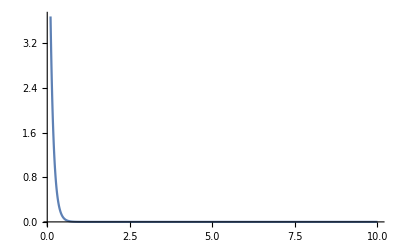

```mathematica
Plot[Exp[-δt / τ]/τ/.τ->0.1,{δt,0.1,10},PlotRange->All]
```

### Pure ohmic case: Unruh-Zurek

Pure ohmic (it’s unphysical because it has no cutoff): 
 -Graphics-

#### Master eq

-Graphics-

#### Coefficients

```mathematica
-Graphics-
-Graphics-
-Graphics-
-Graphics-
```

```mathematica
Series[Coth[β ω/2],{β,0,1}]
```

2/(ω β)+(ω β)/6+O[β]^2

```mathematica
Integrate[1/π ω 2/(ω β) Cos[ω t],{ω,0,Λ}]
Integrate[% Sin[Ω t]Exp[-γ t],t] 
Assuming[t>0&&Ω>0,Series[%,{Λ,∞,0}]//FullSimplify]
```

(2 Sin[t Λ])/(π t β)

1/(2 π β)(ExpIntegralEi[-t (γ-ⅈ (Λ-Ω))]+ExpIntegralEi[-t (γ+ⅈ (Λ-Ω))]-ExpIntegralEi[-t γ-ⅈ t (Λ+Ω)]-ExpIntegralEi[-t γ+ⅈ t (Λ+Ω)])

(ⅇ^(-ⅈ t Λ-t (γ-ⅈ Ω)+O[1/Λ]^2)+ⅇ^(-ⅈ t Λ-t (γ+ⅈ Ω)+O[1/Λ]^2)+ⅇ^(ⅈ t Λ-t (γ+ⅈ Ω)+O[1/Λ]^2)+ⅇ^(ⅈ t Λ+(-t γ+ⅈ t Ω)+O[1/Λ]^2)) O[1/Λ]^1

```mathematica
Exp[-ⅈ t Λ-t (γ-ⅈ Ω)]+Exp[-ⅈ t Λ-t (γ+ⅈ Ω)]+Exp[ⅈ t Λ-t (γ+ⅈ Ω)]+Exp[ⅈ t Λ-t (γ-ⅈ Ω)]//FullSimplify
```

4 ⅇ^(-t γ) Cos[t Λ] Cos[t Ω]

#### From Unruh-Zurek paper

-Graphics-
-Graphics-
-Graphics-

### Markovian case: Caldeira-Leggett (ohmic & at high T)

-Graphics-
From the original Caldeira-Leggett paper, at hight  T  limit:s
-Graphics-
It looks like there's one ħ discrepancy between Caldeira-Legget and the Hu-Path-Zhang paper. I guess Caldeira-Legget is correct, since it gives the right D in the classical limit.

### Wigner equation for the Markovian case, my derivation

The ħ in the diffusion term should be gone. This result is consistent with Caldeira-Leggett.

#### ∂/(∂ t)W(x,p,t)= (-∂/(∂ x){p}+∂/(∂ p){Ω^2 x+2 γ_0 p}+2 γ_0 k_B T ħ∂^2/(∂ p^2))W(x,p,t)

H =1/2 p^2+1/2 Ω^2 x^2
{H, W} =(∂ H)/(∂ x)(∂ W)/(∂ p)-(∂ H)/(∂ p) (∂ W)/(∂ x)=Ω^2 x(∂ W)/(∂ p)-p(∂ W)/(∂ x)

```mathematica
{ħ^2(-ⅈ/ħ),-Ω^2 x (- ⅈ ħ),-2ⅈ ħ γ (-1),-ⅈ 2 k T γ (-ħ^2)}/(ⅈ ħ)
```

{-1,x Ω^2,2 γ,2 ħ k T γ}

#### Langevin equations: ẋ=p ṗ=-2 γ_0 p -Ω^2 x+ξ(t)s

We set m=1

Fokker-Planck (Kramer’s equation):
-Graphics-
-Graphics-(α=γ)

#### ⅈ ħ∂/(∂ t)ρ_r(x-Δ/2,x+Δ/2,t) ={ħ^2∂^2/(∂ x∂ Δ)-Ω^2 x Δ-2ⅈ ħ γ_0 Δ∂/(∂ Δ)-ⅈ 2 k_B T γ_0 Δ^2}ρ_r(x-Δ/2,x+Δ/2,t)

Change of variables:
 y→ x-Δ/2, y'→ x+Δ/2
the inverse transformation is (looks like Keldysh rotation!):
x→ 1/2(y+y') ,Δ→ y'-y
ⅈ ħ∂/(∂ t)ρ_r(x-Δ/2,x+Δ/2,t) ={ħ^2∂^2/(∂ x∂ Δ)-Ω^2 x Δ-2ⅈ ħγ_0 Δ∂/(∂ Δ)-ⅈ 2 k_B Tγ_0 Δ^2}ρ_r(x-Δ/2,x+Δ/2,t)

y-y'=-Δ
y^2-y'^2=-2 x Δ
(y-y')^2=Δ^2
(∂/(∂ y)-∂/(∂ y'))ρ_r(y,y',t) =-2∂/(∂ Δ)ρ_r(y(x,Δ),y'(x,Δ),t)
(∂^2/(∂ y^2)-∂^2/(∂ y'^2))ρ_r(y,y',t) =-2∂^2/(∂ x∂ Δ)ρ_r(y(x,Δ),y'(x,Δ),t)

	∂/(∂ y)ρ_r(y,y',t)={(∂ x)/(∂ y)∂/(∂ x)+(∂ Δ)/(∂ y)∂/(∂ Δ)}ρ_r(y(x,Δ),y'(x,Δ),t)
                                              ={1/2∂/(∂ x)-∂/(∂ Δ)}ρ_r(y(x,Δ),y'(x,Δ),t)
	∂/(∂ y')ρ_r(y,y',t)={1/2∂/(∂ x)+∂/(∂ Δ)}ρ_r(y(x,Δ),y'(x,Δ),t)
	∂^2/(∂ y^2)ρ_r(y,y',t)={1/2∂/(∂ x)-∂/(∂ Δ)}^2 ρ_r(y(x,Δ),y'(x,Δ),t)
              ∂^2/(∂ y'^2)ρ_r(y,y',t)={1/2∂/(∂ x)+∂/(∂ Δ)}^2 ρ_r(y(x,Δ),y'(x,Δ),t)

(∂/(∂ y)+∂/(∂ y'))ρ_r(y,y',t) =∂/(∂ x)ρ_r(y(x,Δ),y'(x,Δ),t)

```mathematica
{y-yp,y^2-yp^2,(y-yp)^2}/.{y-> (x-Δ/2),yp-> (x+Δ/2)}//FullSimplify
```

{-Δ,-2 x Δ,Δ^2}

#### ∂/(∂ Δ)→-ⅈ/ħ p, Δ→- ⅈ ħ ∂/(∂ p) , Δ∂/(∂ Δ)→- ∂/(∂ p) p, Δ^2→-ħ^2∂^2/(∂ p^2)

W(x,p,t)=∫ d Δ  exp(ⅈ/ħ p Δ)   ρ_r(x-Δ/2,x+Δ/2,t)
∂/(∂ t)W(x,p,t)=∫ d Δ  exp(ⅈ/ħ p Δ) ∂/(∂ t)ρ_r(x-Δ/2,x+Δ/2,t)
We can use the replaments:
exp(ⅈ/ħ p Δ)  Δ→  -ⅈ ħ∂/(∂ p)exp(ⅈ/ħ p Δ) 
	exp(ⅈ/ħ p Δ)  Δ^2→ -ħ^2∂^2/(∂ p^2)exp(ⅈ/ħ p Δ) 

∫ d Δ  exp(ⅈ/ħ p Δ)  Δ^2 ρ_r(x-Δ/2,x+Δ/2,t)=-ħ^2∂^2/(∂ p^2)W(x,p,t)
	
∫ d Δ  exp(ⅈ/ħ p Δ)   Δ∂/(∂ Δ)ρ_r(x-Δ/2,x+Δ/2,t)
		= -ⅈ ħ∂/(∂ p)∫ d Δ exp(ⅈ/ħ p Δ) ∂/(∂ Δ)ρ_r(x-Δ/2,x+Δ/2,t)
{integration by parts}
                          =ⅈ ħ∂/(∂ p)∫ d Δ ⅈ/ħ p exp(ⅈ/ħ p Δ) ρ_r(x-Δ/2,x+Δ/2,t)
		=- ∂/(∂ p) p W(x,p,t)
	
∫ d Δ  exp(ⅈ/ħ p Δ)   Δ ρ_r(x-Δ/2,x+Δ/2,t)= -ⅈ ħ ∂/(∂ p)W(x,p,t)
∫ d Δ  exp(ⅈ/ħ p Δ)  ∂^2/(∂ x∂ Δ)ρ_r(x-Δ/2,x+Δ/2,t)=-ⅈ/ħ p∂/(∂ x)W(x,p,t)

```mathematica
D[Exp[ⅈ/ħ p Δ],{p,1}]
D[Exp[ⅈ/ħ p Δ],{p,2}]
```

(ⅈ ⅇ^((ⅈ p Δ)/ħ) Δ)/ħ

-(ⅇ^((ⅈ p Δ)/ħ) Δ^2)/ħ^2

### Non-ohmic, high T, stationary limit

#### η(s)=-1/πΜ γ_0 (ω̃)^-α Λ^(3+α) Gamma[(3+α)/2] Hypergeometric1F1[(3+α)/2,3/2,-1/4 s^2 Λ^2] s, α>-3

η(s)=-∫_0^∞ ⅆω I(ω)  sin(ω s)
	=-2/πΜ γ_0(ω̃)^-α∫_0^∞ ⅆω ω^(α+1)Exp[-ω^2/Λ^2] sin(ω s),                          (I(ω)=2/π Μ γ_0 ω (ω/(ω̃))^α Exp[-ω^2/Λ^2])
	=-1/πΜ γ_0 (ω̃)^-α Λ^(3+α) Gamma[(3+α)/2] Hypergeometric1F1[(3+α)/2,3/2,-1/4 s^2 Λ^2] s

```mathematica
ηintegrand[α_,ω_,Λ_][s_]:=ω^(α+1)  Exp[-ω^2/Λ^2] Sin[ω s]
```

```mathematica
Assuming[Λ>0&&t>0,Integrate[ηintegrand[α,ω,Λ][t],{ω,0,∞}]]//FullSimplify
```

ConditionalExpression[1/2 t Λ^(3+α) Gamma[(3+α)/2] Hypergeometric1F1[(3+α)/2,3/2,-1/4 t^2 Λ^2], Re[α]>-3]

#### ν(s)=2/(π β ℏ)Μ γ_0 (ω̃)^-α Λ^(1+α)Gamma[(1+α)/2] Hypergeometric1F1[(1+α)/2,1/2,-1/4 s^2 Λ^2], α>-1

ν(s)=∫_0^∞ ⅆω I(ω) coth(1/2 β ℏ ω)  cos(ω s)
	≈∫_0^∞ ⅆω I(ω) (1/2 β ℏ ω)^-1  cos(ω s),                                                                                                           (β≈0)
	≈4/(π β ℏ)Μ γ_0(ω̃)^-α∫_0^∞ ⅆω  ⅇ^(-ω^2/Λ^2) ω^α cos(ω s) ,                (I(ω)=2/π Μ γ_0 ω (ω/(ω̃))^α Exp[-ω^2/Λ^2])
	=2/(π β ℏ)Μ γ_0 (ω̃)^-α Λ^(1+α) Gamma[(1+α)/2] Hypergeometric1F1[(1+α)/2,1/2,-1/4 s^2 Λ^2]

```mathematica
νintegrand[α_,ω_,Λ_][s_]:=ω^α  Exp[-ω^2/Λ^2] Cos[ω s]
```

```mathematica
Assuming[Λ>0&&t>0,Integrate[νintegrand[α,ω,Λ][t],{ω,0,∞}]]
```

ConditionalExpression[1/2 Λ^(1+α) Gamma[(1+α)/2] Hypergeometric1F1[(1+α)/2,1/2,-1/4 t^2 Λ^2], Re[α]>-1]

#### At weak coupling: C_∞=-1/(M Ω)2/(π β)Μ γ_0 (ω̃)^-α Λ^α{π (Ω/Λ)^α Tan[(π α)/2]+Ω/Λ Gamma[1/2 (-1+α)]} , α>-1

C_∞≡ℏ/(M Ω)∫_0^∞ ⅆs ν(s) Sin[Ω s]
	=1/(M Ω)2/(π β)Μ γ_0 (ω̃)^-α  ⅇ^(-Ω^2/Λ^2) Λ^α (-ⅈ π  (Ω/Λ)^α-Ω/Λ ExpIntegralE[(1+α)/2,-Ω^2/Λ^2] Gamma[(1+α)/2])
	≈-1/(M Ω)2/(π β)Μ γ_0 (ω̃)^-α Λ^α{π (Ω/Λ)^α Tan[(π α)/2]+Ω/Λ Gamma[1/2 (-1+α)]},              (Λ>>0)

##### Computation

```mathematica
Assuming[Λ>0&&Ω>0,Integrate[Λ^(1+α)Gamma[(1+α)/2] Hypergeometric1F1[(1+α)/2,1/2,-1/4 s^2 Λ^2]Sin[Ω s],{s,0,∞}]]
```

ConditionalExpression[ⅇ^(-Ω^2/Λ^2) Λ^(-1+α) (-ⅈ π Λ (Ω/Λ)^α-Ω ExpIntegralE[(1+α)/2,-Ω^2/Λ^2] Gamma[(1+α)/2]), Re[α]>-1]

```mathematica
c[α_,Λ_,Ω_]:=ⅇ^(-Ω^2/Λ^2) Λ^(-1+α) (-ⅈ π Λ (Ω/Λ)^α-Ω ExpIntegralE[(1+α)/2,-Ω^2/Λ^2] Gamma[(1+α)/2]);
```

```mathematica
Assuming[Ω>0,Series[c[α,Λ,Ω],{Λ,∞,1}]]//FullSimplify
```

Λ^α (-(Ω Gamma[1/2 (-1+α)])/Λ+O[1/Λ]^2)+(-π Ω^α Tan[(π α)/2]+O[1/Λ]^2)

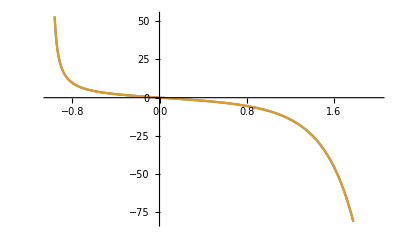

```mathematica
Plot[Evaluate[{c[α,Λ,Ω],-π Ω^α Tan[(π α)/2]-Λ^α(Ω Gamma[1/2 (-1+α)])/Λ}/.Ω-> 1/.Λ->100],{α,-1,2}]
```

```mathematica
c[α,Λ,Ω]/Λ^α/.α->10/.Ω->1/.Λ->1000//N//Chop
```

-0.0116317

##### Numeric check

```mathematica
NIntegrate[Λ^(1+α)Gamma[(1+α)/2] Hypergeometric1F1[(1+α)/2,1/2,-1/4 s^2 Λ^2]Sin[Ω s]/.Ω->1/.α->0.1/.Λ->100,{s,0,1000}]
c[α,Λ,Ω]/.Ω->1/.α->0.1/.Λ->100//N
```

-0.44053

-0.440614-3.60327×10^-15 ⅈ

## Nonlinear QBM

Particle:
-Graphics-
Harmonic oscillator bath:
-Graphics-
Interaction:
-Graphics-
	Linear coupling: k=1, f(x)=x
	Quadratic coupling: k=2
	Cubic coupling: k=3
	Quartic coupling: k=4

### Initial bath in thermal eq

-Graphics-
Hence the influence potential factorizes:
-Graphics-

### Perturbation theory, up to λ^2

F_n[x,x']=Exp{ⅈ/ħ δA_n[x,x']}
The influence action in small λ perturbation:
-Graphics-
where ⟨...⟩_0 is averaging over the bath action, without interaction.

### Quadratic case k=2

Vertex function
-Graphics-
Renormalized potential
-Graphics- 
-Graphics-

### Anharmonic case

-Graphics-
Counterterm:
-Graphics-

-Graphics-

-Graphics-
Typo: (∂ f(x'))/(∂ x')ẋ' 
Use standard approach analogous of deriving the wave function from the path integral (see also derivation in Caldeira-Leggett, page 605-607 ), we get: 

-Graphics-

-Graphics-
-Graphics-

Wigner function definition
-Graphics-
Wigner eq for the anharmonic case:
-Graphics-

```mathematica
Integrate[Exp[-a ξ^2+b ξ]ξ,{ξ,-∞,∞}]
```

ConditionalExpression[(b ⅇ^(b^2/(4 a)) √π)/(2 a^(3/2)), Re[a]>0]

### Semiclassical limit and FP for the anharmonic case

At the semiclassical limit, Wigner eq -> FP eq, 
∂/(∂ t)W = {V_ren,W}+2 γ_o X∂/(∂ p)(X p W)+2 k_B T γ_0 X^2∂^2/(∂ p^2)W
and the asymptotic solution is:
-Graphics-

{V_ren, W} =(∂ V_ren)/(∂ x)(∂ W)/(∂ p)-(∂ V_ren)/(∂ p) (∂ W)/(∂ x)
∂/(∂ p)(X p W)=X W+X p∂/(∂ p)W

∂/(∂ t)W(X,p,t)={ -(∂ V_ren)/(∂ p) ∂/(∂ X)+(∂ V_ren)/(∂ X)∂/(∂ p)+2 γ_o X^2∂/(∂ p)[p ·] +2 k_B T γ_0 X^2∂^2/(∂ p^2)}W(X,p,t)
I think V_ren(X)...

Compare with the one from the classical Brownian motion:
-Graphics-